### 方法一

```mathematica
Gcont=1;
TestInit[m1_,m2_,m3_,initvalues_]:=Block[{x1,y1,x2,y2,x3,y3,vx1,vy1,vx2,vy2,vx3,vy3,R0,P0,E1,E2,E3},{x1,y1,x2,y2,x3,y3,vx1,vy1,vx2,vy2,vx3,vy3}=initvalues;
R0=1/(m1+m2+m3){m1*x1+m2*x2+m3*x3,m1*y1+m2*y2+m3*y3};P0=1/(m1+m2+m3){m1*vx1+m2*vx2+m3*vx3,m1*vy1+m2*vy2+m3*vy3};
E1=1/2 m1 (vx1^2+vy1^2)-Gcont((m1 m2)/(√((x1-x2)^2+(y1-y2)^2))+(m1 m3)/(√((x1-x3)^2+(y1-y3)^2)));E2=1/2 m2 (vx2^2+vy2^2)-Gcont((m1 m2)/(√((x1-x2)^2+(y1-y2)^2))+(m2 m3)/(√((x2-x3)^2+(y2-y3)^2)));E3=1/2 m3 (vx3^2+vy3^2)-Gcont((m3 m2)/(√((x3-x2)^2+(y3-y2)^2))+(m1 m3)/(√((x1-x3)^2+(y1-y3)^2)));Print["Center Position and momentum as :\n",R0,"\n",√(P0.P0),"\n","init Energy as :\n", {E1,E2,E3,E1+E2+E3}];];
ThreeBody[m1_,m2_,m3_,initvalues_]:=Block[{r12,r13,r23,r21,r31,r32,s},r12=((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2);r13=((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2);r23=((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2);r21=-r12;r31=-r13;r32=-r23;
TestInit[m1,m2,m3,initvalues];
s=NDSolve[{Gcont*m2/r12(x1[t]-x2[t])+Gcont*m3/r13(x1[t]-x3[t])==-x1''[t],
Gcont*m2/r12(y1[t]-y2[t])+Gcont*m3/r13(y1[t]-y3[t])==-y1''[t],Gcont*m1/r12(x2[t]-x1[t])+Gcont*m3/r23(x2[t]-x3[t])==-x2''[t],
Gcont*m1/r12(y2[t]-y1[t])+Gcont*m3/r23(y2[t]-y3[t])==-y2''[t],Gcont*m1/r13(x3[t]-x1[t])+Gcont*m2/r23(x3[t]-x2[t])==-x3''[t],Gcont*m1/r13(y3[t]-y1[t])+Gcont*m2/r23(y3[t]-y2[t])==-y3''[t],
Reduce[{x1[0],y1[0],x2[0],y2[0],x3[0],y3[0],x1'[0],y1'[0],x2'[0],y2'[0],x3'[0],y3'[0]}==initvalues]},{x1,x2,x3,y1,y2,y3},{t,0,200}]]
```

Center Position and momentum as :
{0,10/(3 √3)}
0.
init Energy as :
{5-10 √3,-8.66025,-8.66025,-29.641}

NDSolve::ndsz: 在 t == 102.938 处，步长实际上为零；可能存在奇点或者刚性系统.

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…],x3→InterpolatingFunction[…],y1→InterpolatingFunction[…],y2→InterpolatingFunction[…],y3→InterpolatingFunction[…]}}

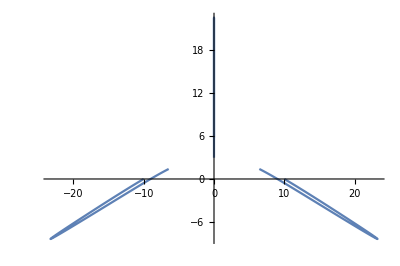

```mathematica
s=ThreeBody[10,10,10,{0,10*Tan[30°],10,0,-10,0,0,1,√3/2,-0.5,-√3/2,-0.5}]
ParametricPlot[{{x1[t],y1[t]},{x2[t],y2[t]},{x3[t],y3[t]}}/.s,{t,0,100}]
```

```mathematica
TestInit[10,10,10,Flatten[{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t],x1'[t],y1'[t],x2'[t],y2'[t],x3'[t],y3'[t]}/.s/.t->80]]
```

Center Position and momentum as :
{0.,1.9245}
0.
init Energy as :
{-6.08023,-5.40534,-5.40534,-16.8909}

### 方法二

```mathematica
(*https://blog.stephenwolfram.com/2017/08/when-exactly-will-the-eclipse-happen-a-multimillenium-tale-of-computation/*)
```

```mathematica
ThreeBody2[ndim_]:=Block[{eqns,inits,sols},
{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3]}=RandomReal[{0,1},3];
eqns={Subscript[m, 1] Subscript[r, 1]''[t]==-(Subscript[m, 1] Subscript[m, 2] (Subscript[r, 1][t]-Subscript[r, 2][t]))/Norm[Subscript[r, 1][t]-Subscript[r, 2][t]]^3-(Subscript[m, 1] Subscript[m, 3] (Subscript[r, 1][t]-Subscript[r, 3][t]))/Norm[Subscript[r, 1][t]-Subscript[r, 3][t]]^3,Subscript[m, 2] Subscript[r, 2]''[t]==-(Subscript[m, 1] Subscript[m, 2] (Subscript[r, 2][t]-Subscript[r, 1][t]))/Norm[Subscript[r, 2][t]-Subscript[r, 1][t]]^3-(Subscript[m, 2] Subscript[m, 3] (Subscript[r, 2][t]-Subscript[r, 3][t]))/Norm[Subscript[r, 2][t]-Subscript[r, 3][t]]^3,Subscript[m, 3] Subscript[r, 3]''[t]==-(Subscript[m, 1] Subscript[m, 3] (Subscript[r, 3][t]-Subscript[r, 1][t]))/Norm[Subscript[r, 3][t]-Subscript[r, 1][t]]^3-(Subscript[m, 2] Subscript[m, 3] (Subscript[r, 3][t]-Subscript[r, 2][t]))/Norm[Subscript[r, 3][t]-Subscript[r, 2][t]]^3};
inits=Table[{Subscript[r, i][0]==RandomReal[{-1,1},ndim],Subscript[r, i]'[0]==RandomReal[{-1,1},ndim]},{i,3}];sols=NDSolve[{eqns,inits},{Subscript[r, 1],Subscript[r, 2],Subscript[r, 3]},{t,0,100},AccuracyGoal->10];
Switch[ndim,
2,ParametricPlot[Evaluate[{Subscript[r, 1][t],Subscript[r, 2][t],Subscript[r, 3][t]}/.First[sols]],{t,0,10}],
3,ParametricPlot3D[Evaluate[{Subscript[r, 1][t],Subscript[r, 2][t],Subscript[r, 3][t]}/.First[sols]],{t,0,10}]]]
```

```mathematica
ThreeBody2[3]
```

-Graphics3D-